```mathematica
EuclidPrimeQ[n_Integer?Positive] := Fold[And[#1,Mod[n,#2] ≠ 0]&, True, Range[2,Floor[Sqrt[n]]]]
```

```mathematica
EuclidPrimeQ::"usage" = "EuclidPrimeQ[n] tells whether a number is prime by testing all divisors less than Sqrt[n]"
```

EuclidPrimeQ[n] tells whether a number is prime by testing all divisors less than Sqrt[n]

```mathematica
Select[Range[2,100],EuclidPrimeQ]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
LucasPrimeQ[n_Integer?Positive]:= 
Module[{foo},
foo[a_]:=Fold[And[#1, PowerMod[a,#2 , n] ≠ 1]&, True, Rest[Reverse[Divisors[n-1]]]];
Fold[Or[#1, And[PowerMod[#2,(n-1),n]==1, foo[#2]]]&,False,Range[1,n]]]
```

```mathematica
Select[Range[2,100],LucasPrimeQ]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
LucasPrimeQ::"usage" = "LucasPrimeQ[n] tells whether a number is prime by testing whether there is an element of order n-1."
```

LucasPrimeQ[n] tells whether a number is prime by testing whether there is an element of order n-1.

```mathematica
ProthPrimeQ[nn_Integer]:= Module[{foo,bar},foo[n_] := Map[{n/#,#}&,Table[2^i,{i,1,Floor[Log2[n]]}]];
bar[lst_] :=  If[lst =={}, False, If[IntegerQ[lst[[1]][[1]]] && lst[[1]][[1]] < lst[[1]][[2]], True, bar[Rest[lst]]]];
If[bar[foo[nn-1]], Fold[Or[#1, PowerMod[#2,(nn-1)/2,nn] == nn -1]&,False,Range[1,nn-1]], EuclidPrimeQ[nn]]]
```

```mathematica
ProthPrimeQ::"usage" = "ProthPrimeQ decides whether a number of the form k*2^s + 1 is prime."
```

ProthPrimeQ decides whether a number of the form k*2^s + 1 is prime.

```mathematica
ProthPrimeQ[100]
```

False

```mathematica
PocklingtonPrimeQ[n_Integer] := Module[{foo=FactorInteger[n-1], bar,baz, bletch}, bar = Power @@ foo[[1]]; baz = Map[First,Rest[foo]];
bletch[a_] := Fold[And[#1,GCD[n,#2] ==1]&, True,Map[a^((n-1)/#)-1&,baz]];
If[baz =={},bar=1; baz ={foo[[1]][[1]] }];n==2 || n==3 || Fold[Or[#1,And[PowerMod[#2,n-1,n] == 1, bletch[#2]]]&, False,Range[bar,n]]]
```

```mathematica
PocklingtonPrimeQ::"usage" = "PocklingtonPrimeQ[n] decides whether n is prime based on a partial factorization of n-1"
```

PocklingtonPrimeQ[n] decides whether n is prime based on a partial factorization of n-1

```mathematica
Select[Range[2,100],PocklingtonPrimeQ]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,49,53,59,61,67,71,73,79,83,89,97}

```mathematica
LucasKraitchikLemerPrimeQ[n_Integer]:= Module[{foo=Map[First,FactorInteger[n-1]], bar},bar[a_] := Fold[And[#1, PowerMod[a,(n-1)/#2 , n] ≠ 1]&, True,foo];Or[n ==2, n==3, Fold[Or[#1,And[PowerMod[#2,n-1,n] == 1,bar[#2]]]&,False,Range[1,n]]]]
```

```mathematica
LucasKraitchikLemerPrimeQ::"usage" = "LucasKraitchikLemerPrimeQ[n] decides whether n is prime based on the factorization of n-1."
```

LucasKraitchikLemerPrimeQ[n] decides whether n is prime based on the factorization of n-1.

```mathematica
SelfridgePrimeQ::"usage" ="SelfridgePrimeQ[n] decides whether n is prime based on the factorization of n-1."
```

```mathematica
SelfridgePrimeQ[n_Integer]:=Module[{x=Map[#[[1]]&,FactorInteger[n-1]],y},
y[a_]:=Fold[And[#1,PowerMod[a,(n-1)/#2,n]≠1]&,True,x];
Or[n==2, n==3, Fold[Or[#1,And[PowerMod[#2,n-1,n] ==1,y[#2]]]&,False,Range[1,n]]]]
```

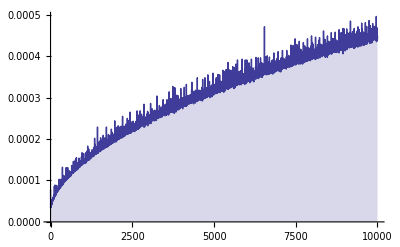

```mathematica
DiscretePlot[Timing[EuclidPrimeQ[Prime[i]]][[1]],{i,1,10000}]
```

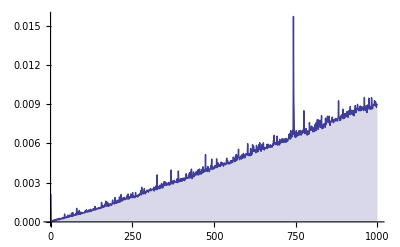

```mathematica
DiscretePlot[Timing[LucasPrimeQ[Prime[i]]][[1]],{i,1,1000}]
```

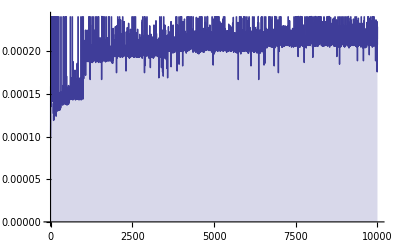

```mathematica
DiscretePlot[Timing[ProthPrimeQ[Prime[i]]][[1]],{i,1,10000}]
```

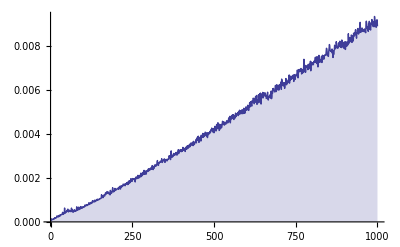

```mathematica
DiscretePlot[Timing[SelfridgePrimeQ[Prime[i]]][[1]],{i,1,1000}]
```